```mathematica
SetDirectory[NotebookDirectory[]];
```

## p10q3

```mathematica
datadir="../Processed_Data/5_MagneticCatalysis_CDW";
```

```mathematica
a0v0d44data=Import[StringJoin[datadir,"/p10q3n4a0_V0.44_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d44data=Import[StringJoin[datadir,"/p10q3n4a0.2_V0.44_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d44data=Import[StringJoin[datadir,"/p10q3n4a0.4_V0.44_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d5v0d44data=Import[StringJoin[datadir,"/p10q3n4a0.5_V0.44_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d44data=Import[StringJoin[datadir,"/p10q3n4a0.6_V0.44_CDWOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v0d4data=Import[StringJoin[datadir,"/p10q3n4a0_V0.4_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d4data=Import[StringJoin[datadir,"/p10q3n4a0.2_V0.4_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d4data=Import[StringJoin[datadir,"/p10q3n4a0.4_V0.4_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d5v0d4data=Import[StringJoin[datadir,"/p10q3n4a0.5_V0.4_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d4data=Import[StringJoin[datadir,"/p10q3n4a0.6_V0.4_CDWOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v0d5data=Import[StringJoin[datadir,"/p10q3n4a0_V0.5_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d5data=Import[StringJoin[datadir,"/p10q3n4a0.2_V0.5_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d5data=Import[StringJoin[datadir,"/p10q3n4a0.4_V0.5_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d5v0d5data=Import[StringJoin[datadir,"/p10q3n4a0.5_V0.5_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d5data=Import[StringJoin[datadir,"/p10q3n4a0.6_V0.5_CDWOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v0d44data=a0v0d44data[[;;,Ordering[a0v0d44data[[1]]]]];
a0d2v0d44data=a0d2v0d44data[[;;,Ordering[a0d2v0d44data[[1]]]]];
a0d4v0d44data=a0d4v0d44data[[;;,Ordering[a0d4v0d44data[[1]]]]];
a0d5v0d44data=a0d5v0d44data[[;;,Ordering[a0d5v0d44data[[1]]]]];
a0d6v0d44data=a0d6v0d44data[[;;,Ordering[a0d6v0d44data[[1]]]]];
```

```mathematica
a0v0d4data=a0v0d4data[[;;,Ordering[a0v0d4data[[1]]]]];
a0d2v0d4data=a0d2v0d4data[[;;,Ordering[a0d2v0d4data[[1]]]]];
a0d4v0d4data=a0d4v0d4data[[;;,Ordering[a0d4v0d4data[[1]]]]];
a0d5v0d4data=a0d5v0d4data[[;;,Ordering[a0d5v0d4data[[1]]]]];
a0d6v0d4data=a0d6v0d4data[[;;,Ordering[a0d6v0d4data[[1]]]]];
```

```mathematica
a0v0d5data=a0v0d5data[[;;,Ordering[a0v0d5data[[1]]]]];
a0d2v0d5data=a0d2v0d5data[[;;,Ordering[a0d2v0d5data[[1]]]]];
a0d4v0d5data=a0d4v0d5data[[;;,Ordering[a0d4v0d5data[[1]]]]];
a0d5v0d5data=a0d5v0d5data[[;;,Ordering[a0d5v0d5data[[1]]]]];
a0d6v0d5data=a0d6v0d5data[[;;,Ordering[a0d6v0d5data[[1]]]]];
```

```mathematica
numplaqs=421;
```

```mathematica
psize=0.03;
lthickness=0.006;
```

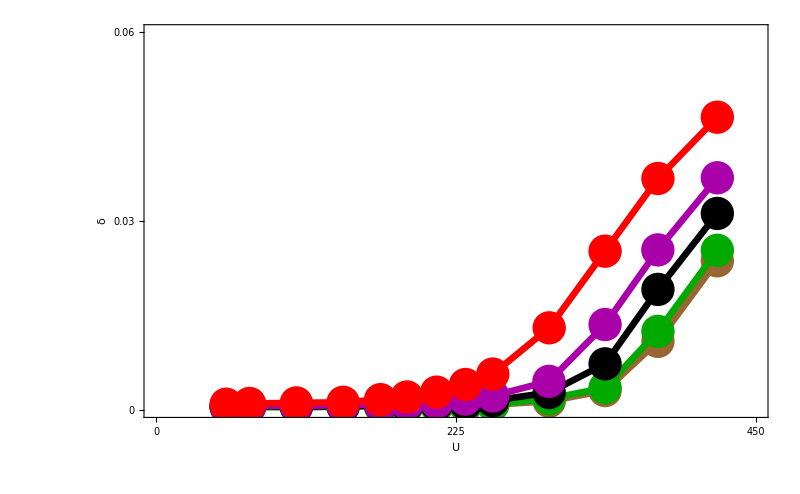

```mathematica
xrange={0,450};
yrange={0,0.06};
Show[
ListPlot[Transpose@{numplaqs*a0v0d44data[[1]],a0v0d44data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d44data[[1]],a0v0d44data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d44data[[1]],a0d2v0d44data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d44data[[1]],a0d2v0d44data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d44data[[1]],a0d4v0d44data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d44data[[1]],a0d4v0d44data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d5v0d44data[[1]],a0d5v0d44data[[2]]},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d5v0d44data[[1]],a0d5v0d44data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d44data[[1]],a0d6v0d44data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d44data[[1]],a0d6v0d44data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"U\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.03,0.06},None},{{0,225,450},None}},FrameTicksStyle->FontSize->50
]
```

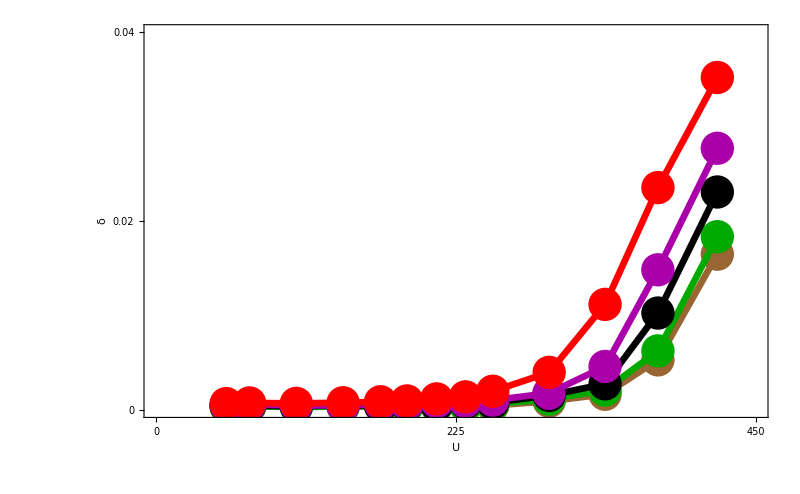

```mathematica
xrange={0,450};
yrange={0,0.04};
Show[
ListPlot[Transpose@{numplaqs*a0v0d4data[[1]],a0v0d4data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d4data[[1]],a0v0d4data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d4data[[1]],a0d2v0d4data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d4data[[1]],a0d2v0d4data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d4data[[1]],a0d4v0d4data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d4data[[1]],a0d4v0d4data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d5v0d4data[[1]],a0d5v0d4data[[2]]},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d5v0d4data[[1]],a0d5v0d4data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d4data[[1]],a0d6v0d4data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d4data[[1]],a0d6v0d4data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"U\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.02,0.04},None},{{0,225,450},None}},FrameTicksStyle->FontSize->50
]
```

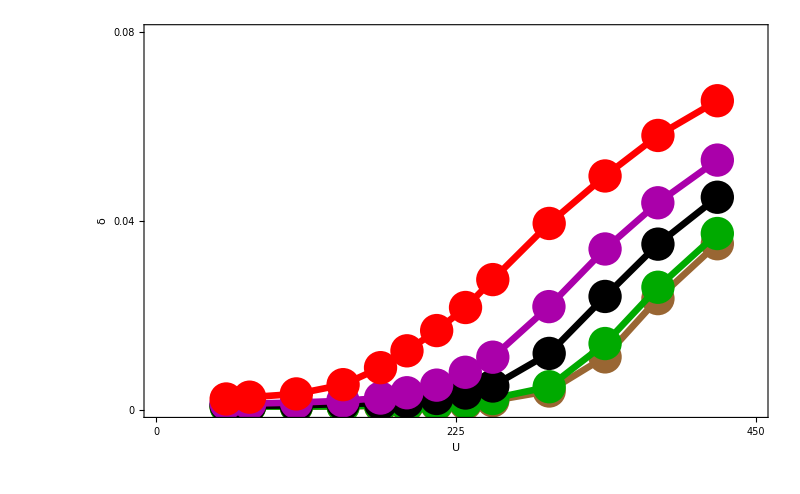

```mathematica
xrange={0,450};
yrange={0,0.08};
Show[
ListPlot[Transpose@{numplaqs*a0v0d5data[[1]],a0v0d5data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d5data[[1]],a0v0d5data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d5data[[1]],a0d2v0d5data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d5data[[1]],a0d2v0d5data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d5data[[1]],a0d4v0d5data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d5data[[1]],a0d4v0d5data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d5v0d5data[[1]],a0d5v0d5data[[2]]},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d5v0d5data[[1]],a0d5v0d5data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d5data[[1]],a0d6v0d5data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d5data[[1]],a0d6v0d5data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"U\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.04,0.08},None},{{0,225,450},None}},FrameTicksStyle->FontSize->50
]
```

## p14q3

```mathematica
datadir="../Processed_Data/5_MagneticCatalysis_CDW";
```

```mathematica
a0v0d3data=Import[StringJoin[datadir,"/p14q3n3a0_V0.3_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d3data=Import[StringJoin[datadir,"/p14q3n3a0.2_V0.3_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d3data=Import[StringJoin[datadir,"/p14q3n3a0.4_V0.3_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d3data=Import[StringJoin[datadir,"/p14q3n3a0.6_V0.3_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d8v0d3data=Import[StringJoin[datadir,"/p14q3n3a0.8_V0.3_CDWOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v0d4data=Import[StringJoin[datadir,"/p14q3n3a0_V0.4_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d4data=Import[StringJoin[datadir,"/p14q3n3a0.2_V0.4_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d4data=Import[StringJoin[datadir,"/p14q3n3a0.4_V0.4_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d4data=Import[StringJoin[datadir,"/p14q3n3a0.6_V0.4_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d7v0d4data=Import[StringJoin[datadir,"/p14q3n3a0.7_V0.4_CDWOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v0d5data=Import[StringJoin[datadir,"/p14q3n3a0_V0.5_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d5data=Import[StringJoin[datadir,"/p14q3n3a0.2_V0.5_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d5data=Import[StringJoin[datadir,"/p14q3n3a0.4_V0.5_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d5v0d5data=Import[StringJoin[datadir,"/p14q3n3a0.5_V0.5_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d5data=Import[StringJoin[datadir,"/p14q3n3a0.6_V0.5_CDWOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v0d3data=a0v0d3data[[;;,Ordering[a0v0d3data[[1]]]]];
a0d2v0d3data=a0d2v0d3data[[;;,Ordering[a0d2v0d3data[[1]]]]];
a0d4v0d3data=a0d4v0d3data[[;;,Ordering[a0d4v0d3data[[1]]]]];
a0d6v0d3data=a0d6v0d3data[[;;,Ordering[a0d6v0d3data[[1]]]]];
a0d8v0d3data=a0d8v0d3data[[;;,Ordering[a0d8v0d3data[[1]]]]];
```

```mathematica
a0v0d4data=a0v0d4data[[;;,Ordering[a0v0d4data[[1]]]]];
a0d2v0d4data=a0d2v0d4data[[;;,Ordering[a0d2v0d4data[[1]]]]];
a0d4v0d4data=a0d4v0d4data[[;;,Ordering[a0d4v0d4data[[1]]]]];
a0d6v0d4data=a0d6v0d4data[[;;,Ordering[a0d6v0d4data[[1]]]]];
a0d7v0d4data=a0d7v0d4data[[;;,Ordering[a0d7v0d4data[[1]]]]];
```

```mathematica
a0v0d5data=a0v0d5data[[;;,Ordering[a0v0d5data[[1]]]]];
a0d2v0d5data=a0d2v0d5data[[;;,Ordering[a0d2v0d5data[[1]]]]];
a0d4v0d5data=a0d4v0d5data[[;;,Ordering[a0d4v0d5data[[1]]]]];
a0d5v0d5data=a0d5v0d5data[[;;,Ordering[a0d5v0d5data[[1]]]]];
a0d6v0d5data=a0d6v0d5data[[;;,Ordering[a0d6v0d5data[[1]]]]];
```

```mathematica
numplaqs=155;
```

```mathematica
psize=0.03;
lthickness=0.006;
```

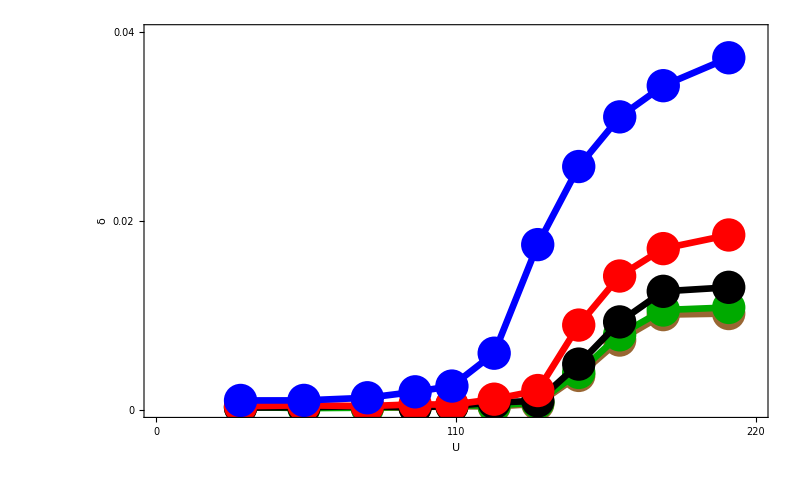

```mathematica
xrange={0,220};
yrange={0,0.04};
Show[
ListPlot[Transpose@{numplaqs*a0v0d3data[[1]],a0v0d3data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d3data[[1]][[;;-8]],a0v0d3data[[2]][[;;-8]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d3data[[1]],a0d2v0d3data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d3data[[1]][[;;-8]],a0d2v0d3data[[2]][[;;-8]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d3data[[1]],a0d4v0d3data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d3data[[1]][[;;-8]],a0d4v0d3data[[2]][[;;-8]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d3data[[1]],a0d6v0d3data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d3data[[1]][[;;-8]],a0d6v0d3data[[2]][[;;-8]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d8v0d3data[[1]],a0d8v0d3data[[2]]},PlotStyle->{Blue,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d8v0d3data[[1]][[;;-2]],a0d8v0d3data[[2]][[;;-2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"U\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.02,0.04},None},{{0,110,220},None}},FrameTicksStyle->FontSize->50
]
```

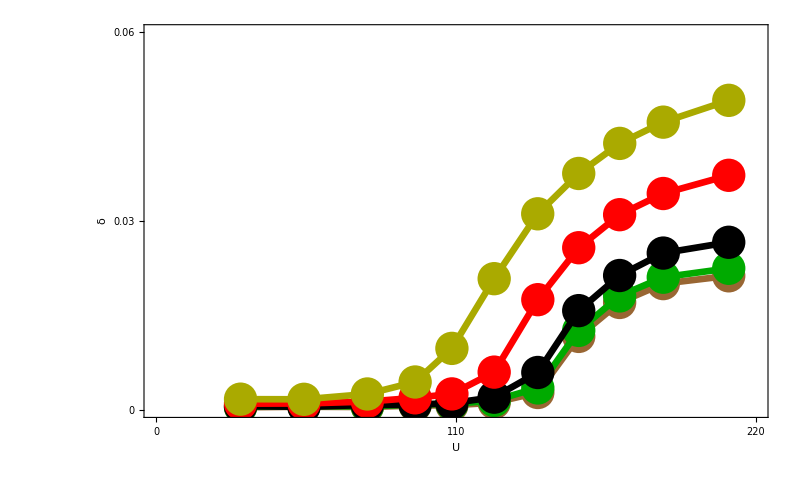

```mathematica
xrange={0,220};
yrange={0,0.06};
Show[
ListPlot[Transpose@{numplaqs*a0v0d4data[[1]],a0v0d4data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d4data[[1]][[;;-8]],a0v0d4data[[2]][[;;-8]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d4data[[1]],a0d2v0d4data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d4data[[1]][[;;-8]],a0d2v0d4data[[2]][[;;-8]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d4data[[1]],a0d4v0d4data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d4data[[1]][[;;-8]],a0d4v0d4data[[2]][[;;-8]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d4data[[1]],a0d6v0d4data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d4data[[1]][[;;-8]],a0d6v0d4data[[2]][[;;-8]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d7v0d4data[[1]],a0d7v0d4data[[2]]},PlotStyle->{Darker[Yellow],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d7v0d4data[[1]][[;;-2]],a0d7v0d4data[[2]][[;;-2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Yellow],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"U\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.03,0.06},None},{{0,110,220},None}},FrameTicksStyle->FontSize->50
]
```

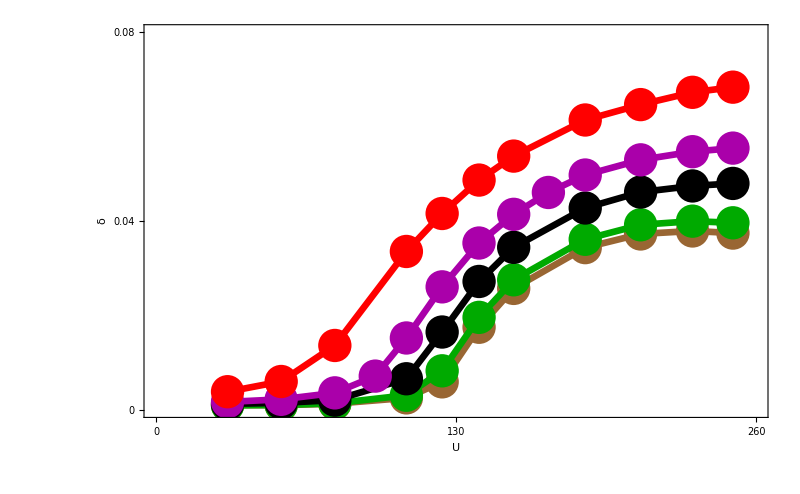

```mathematica
xrange={0,260};
yrange={0,0.08};
Show[
ListPlot[Transpose@{numplaqs*a0v0d5data[[1]],a0v0d5data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d5data[[1]][[;;-8]],a0v0d5data[[2]][[;;-8]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d5data[[1]],a0d2v0d5data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d5data[[1]][[;;-8]],a0d2v0d5data[[2]][[;;-8]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d5data[[1]],a0d4v0d5data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d5data[[1]][[;;-8]],a0d4v0d5data[[2]][[;;-8]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d5v0d5data[[1]],a0d5v0d5data[[2]]},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d5v0d5data[[1]][[;;-2]],a0d5v0d5data[[2]][[;;-2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d5data[[1]],a0d6v0d5data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d5data[[1]][[;;-8]],a0d6v0d5data[[2]][[;;-8]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"StyleBox[\"U\",FontSize->36]","StyleBox[\"δ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.04,0.08},None},{{0,130,260},None}},FrameTicksStyle->FontSize->50
]
```

## Honeycomb

```mathematica
datadir="../Processed_Data/5_MagneticCatalysis_CDW";
```

```mathematica
a0v0d2data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0_V0.2_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d2data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.2_V0.2_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d2data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.4_V0.2_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d2data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.6_V0.2_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d8v0d2data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.8_V0.2_CDWOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v0d3data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0_V0.3_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d3data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.2_V0.3_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d3data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.4_V0.3_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d3data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.6_V0.3_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d8v0d3data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.8_V0.3_CDWOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
a0v0d4data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0_V0.4_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d2v0d4data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.2_V0.4_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d4v0d4data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.4_V0.4_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d6v0d4data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.6_V0.4_CDWOrderFunctionMagneticFlux.txt"],"Data"];
a0d8v0d4data=Import[StringJoin[datadir,"/honeycombOBC_nl20a0.8_V0.4_CDWOrderFunctionMagneticFlux.txt"],"Data"];
```

```mathematica
numplaqs=1141;
```

```mathematica
psize=0.03;
lthickness=0.006;
```

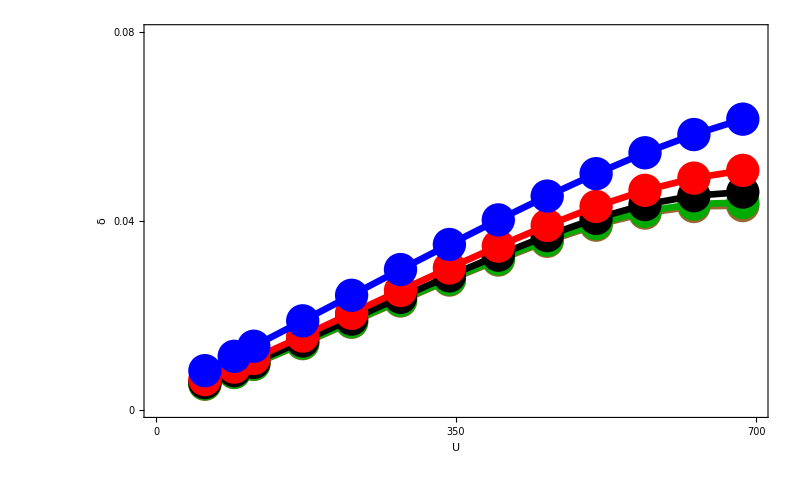

```mathematica
xrange={0,700};
yrange={0,0.08};
Show[
ListPlot[Transpose@{numplaqs*a0v0d2data[[1]],a0v0d2data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d2data[[1]],a0v0d2data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d2data[[1]],a0d2v0d2data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d2data[[1]],a0d2v0d2data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d2data[[1]],a0d4v0d2data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d2data[[1]],a0d4v0d2data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d2data[[1]],a0d6v0d2data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d2data[[1]],a0d6v0d2data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d8v0d2data[[1]],a0d8v0d2data[[2]]},PlotStyle->{Blue,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d8v0d2data[[1]],a0d8v0d2data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.04,0.08},None},{{0,350,700},None}},FrameTicksStyle->FontSize->50
]
```

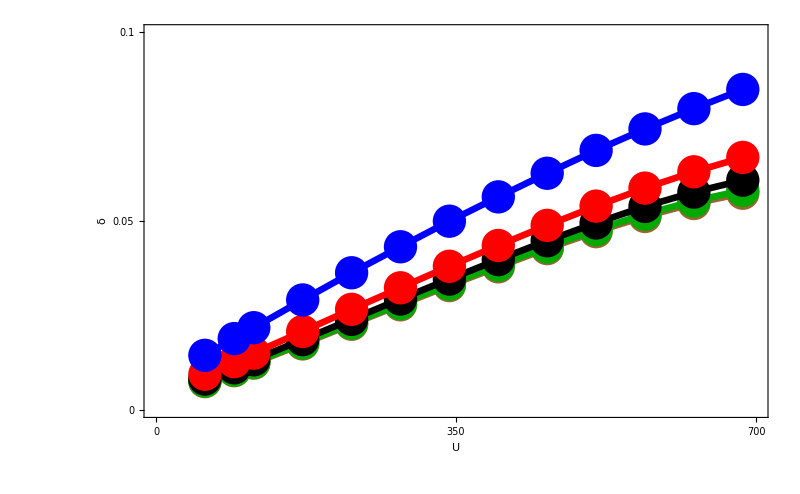

```mathematica
xrange={0,700};
yrange={0,0.1};
Show[
ListPlot[Transpose@{numplaqs*a0v0d3data[[1]],a0v0d3data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d3data[[1]],a0v0d3data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d3data[[1]],a0d2v0d3data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d3data[[1]],a0d2v0d3data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d3data[[1]],a0d4v0d3data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d3data[[1]],a0d4v0d3data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d3data[[1]],a0d6v0d3data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d3data[[1]],a0d6v0d3data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d8v0d3data[[1]],a0d8v0d3data[[2]]},PlotStyle->{Blue,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d8v0d3data[[1]],a0d8v0d3data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.05,0.1},None},{{0,350,700},None}},FrameTicksStyle->FontSize->50
]
```

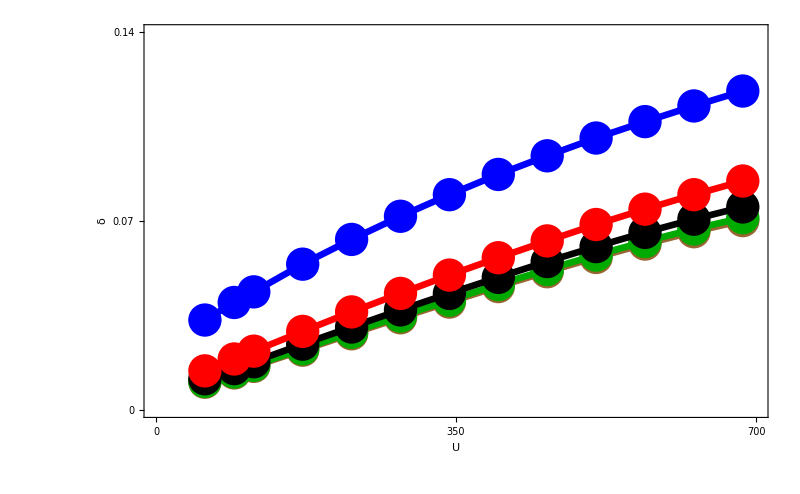

```mathematica
xrange={0,700};
yrange={0,0.14};
Show[
ListPlot[Transpose@{numplaqs*a0v0d4data[[1]],a0v0d4data[[2]]},PlotStyle->{Brown,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0v0d4data[[1]],a0v0d4data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d2v0d4data[[1]],a0d2v0d4data[[2]]},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d2v0d4data[[1]],a0d2v0d4data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d4v0d4data[[1]],a0d4v0d4data[[2]]},PlotStyle->{Black,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d4v0d4data[[1]],a0d4v0d4data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d6v0d4data[[1]],a0d6v0d4data[[2]]},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d6v0d4data[[1]],a0d6v0d4data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{numplaqs*a0d8v0d4data[[1]],a0d8v0d4data[[2]]},PlotStyle->{Blue,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{numplaqs*a0d8v0d4data[[1]],a0d8v0d4data[[2]]},Joined->True,InterpolationOrder->1,PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.07,0.14},None},{{0,350,700},None}},FrameTicksStyle->FontSize->50
]
```